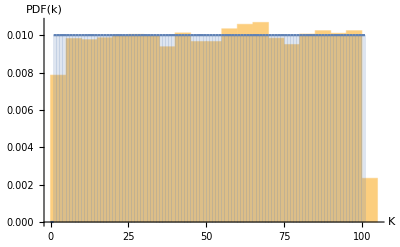
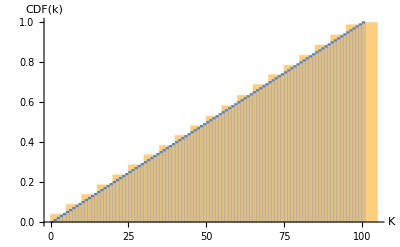
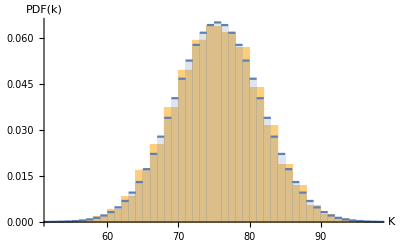
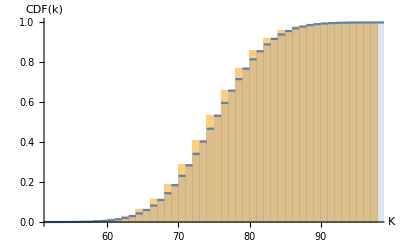
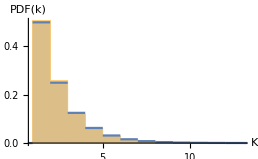
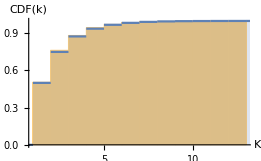
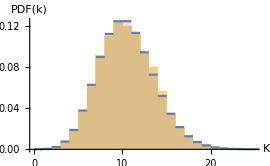
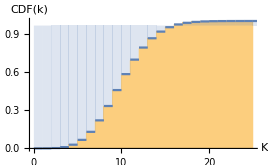
Distribution | PDF | PDF Histogram | CDF Histogram | Mean | Variance
discrete_uniform | Piecewise[{{1/100, 1≤k≤100}, {0, True}}] | -Graphics- | -Graphics- | 50.9101 | 834.546
binomial | Piecewise[{{7.00649×10^-46 Binomial[150, k], 0≤k≤150}, {0, True}}] | -Graphics- | -Graphics- | 74.9451 | 37.5422
geometric | Piecewise[{{0.5^k, k≥1}, {0, True}}] | -Graphics- | -Graphics- | 1.9609 | 1.88576
poisson | Piecewise[{{10^k/(ⅇ^10 k!), k≥0}, {0, True}}] | -Graphics- | -Graphics- | 10.0387 | 10.0088
logarithmic | Piecewise[{{(1.4427 0.5^k)/k, k≥1}, {0, True}}] | -Graphics- | -Graphics- | 1.441 | 0.795599

```mathematica
f[arg_]:=(
str=OpenRead["Visual Studio 2013/Projects/StatMod/"<>arg<>".txt"];
pdf=Read[str, Expression];
mean=Read[str, Number];
variance=Read[str, Number];
data=ReadList[str, Number,10000];
Close[str];
{
arg,
pdf//TraditionalForm,
Show[Histogram[data, 20, "PDF", AxesLabel->{"K","PDF(k)"}], DiscretePlot[pdf, {k,0, 100}, ExtentSize->Right]],
Show[Histogram[data, 20, "CDF", AxesLabel->{"K","CDF(k)"}], DiscretePlot[Sum[pdf, {k, 0, n}], {n,0, 100}, ExtentSize->Right]],
mean,
variance
}
)

Grid[Prepend[Table[f[arg], {arg, {"discrete_uniform", "binomial", "geometric", "poisson", "logarithmic"}}],{"Distribution", "PDF", "PDF Histogram", "CDF Histogram", "Mean", "Variance"}]]
```